```mathematica
(* Notebook for analysing the bahaviour of massless particles incident on the magnetic vector potential of a simple conducting wire loop *)
```

```mathematica
(*Initialise wire loop magnetic field using the expression computed from the Biot-Savart Law*)
ClearAll["Global`*"];
β=0.2;(* Wire loop parameter *)
a=1;(*radius of wire loop*)
g=1;
B[r_]:=(g a^2)/(4π)NIntegrate[(a^2-r a Cos[ϕ])/((r^2+(β a)^2+a^2-2 a r Cos[ϕ])^(3/2)),{ϕ,0,2π}];
(*Plot3D[B[Sqrt[x^2+y^2]],{x,-2a,2a},{y,-2a,2a},AxesLabel->{x,y,"B(r)"},ColorFunction->"ThermometerColors",PlotLegends->Automatic,LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],Boxed->False,ImageSize->Full]*)
```

```mathematica
(*Derive the magnetic vector potential by applying the relevant components of the curl operator and solve.*)
s=NDSolve[{D[V[r],r]+V[r]/r==B[r],V[0.001]==0},V,{r,0.001,10000}];
V=First[V/.s];
```

NIntegrate::inumr: The integrand (1-r Cos[ϕ])/((1.04+r^2-2 r Cos[ϕ])^(3/2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NDSolve::nbnum1: The function value -0.002 Im[Cos[ϕ]]==0 is not True or False when the arguments are {0.001,0.,0.471433}.

NDSolve::nbnum1: The function value 1.04-0.002 Re[Cos[ϕ]]≤0 is not True or False when the arguments are {0.001,0.,0.471433}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

NDSolve::ecboo: The value of event condition function at r = 0.001 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at r = 0.00100002 was not True or False. The event will be considered inactive.

NDSolve::ecboo: The value of event condition function at r = 0.00100005 was not True or False. The event will be considered inactive.

General::stop: Further output of NDSolve::ecboo will be suppressed during this calculation.

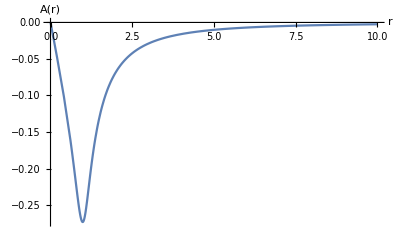

```mathematica
(*Plot the magnetic vector potential*)
Plot[-V[r],{r,0.001,10a},AxesLabel->{"r","A(r)"},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->{{0,5.2},{0.01,-0.30}}]
```

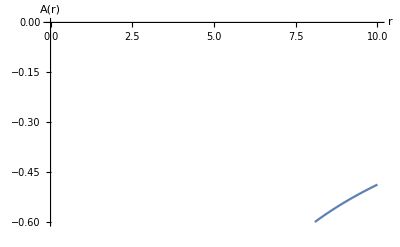

```mathematica
(* Lorentzian approximation of the scalar potential *)
v=-100;a=1;β=0.2;k=0.1;m=1;
(* U[r_]:=(v r^m)/((1+(r/a)^2)^m);*)
G[r_]:=(1-Exp[-2*NIntegrate[V[x],{x,r,10000}]])
U[r_]:=-10*G[r];
Plot[U[r],{r,0.1,10a},AxesLabel->{"r","A(r)"},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->{{0,10},{-0.6,0}}]
```

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

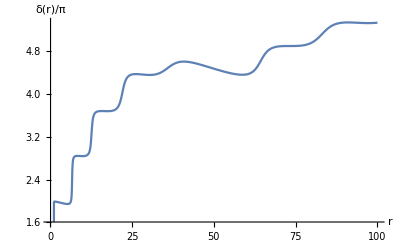

```mathematica
(* Calculate the phase shift *)
k=0.1;
iterations=5;
p[r_]:=BesselJ[m,k r]Cos[δ[r]]-BesselY[m,k r]Sin[δ[r]];
JPRIME[r_]:=1/2(BesselJ[m-1,k*r]-BesselJ[m+1,k*r]);
YPRIME[r_]:=1/2(BesselY[m-1,k*a]-BesselY[m+1,k*r]);
q[r_]:=JPRIME[r]Cos[δ[r]]-YPRIME[r]Sin[δ[r]];
For[i=0,i<iterations,i++,δtemp=NDSolveValue[{δ'[r]==(r π)/2 p[r]((U'[r])/(k-U[r])(q[r]-m/r p[r])+((U[r])^2-2k U[r])p[r]),δ[0.1]==0},δ,{r,0.1,100}];
δ[r]=δtemp[r];]
Plot[δ[r]/π,{r,0.1,100},AxesLabel->{r,"δ(r)/π"}]
```

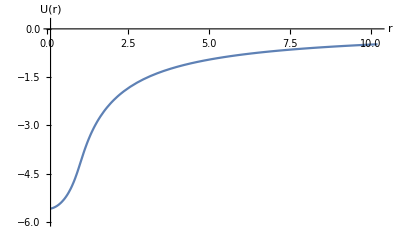

```mathematica
Plot[U[r],{r,0.1,10.2},AxesLabel->{"r","U(r)"},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48],PlotRange->{{0.1,10.2},{-6,0.2}}]
Plot[δ[r]/π,{r,0.1,100},AxesLabel->{r,"δ(r)/π"},PlotRange->{{0.1,8},{0,4.2}},LabelStyle->Directive[Black,FontSize->48],TicksStyle->Directive[Black,FontSize->48]]
```